```mathematica
SatisfiabilityInstances
```

```mathematica
lr
```

```mathematica
1+1
```

2

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/fourer.m"];
```

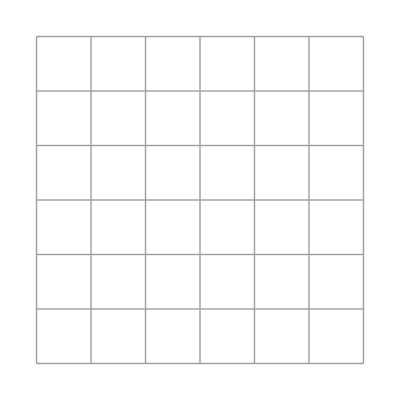

```mathematica
Get["/Users/johncosnett/Dropbox/05_PROGRAMS/001_LIFE/fourer.m"];
looker2=plt[({{xNW11, xN11, xN12, xN13, xN14, xNE14}, {xW11, x11, x12, x13, x14, xE14}, {xW21, x21, x22, x23, x24, xE24}, {xW31, x31, x32, x33, x34, xE34}, {xW41, x41, x42, x43, x44, xE44}, {xSW41, xS41, xS42, xS43, xS44, xSE44}})/.#]&;
(*X0=IntegerPart@ImageData@(looker2/@endGame)[[1]];*)
looker2/@endGame
```

```mathematica
life44
```

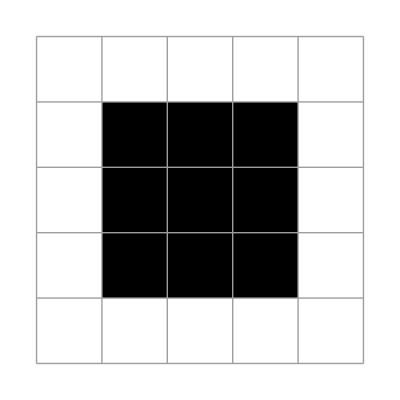
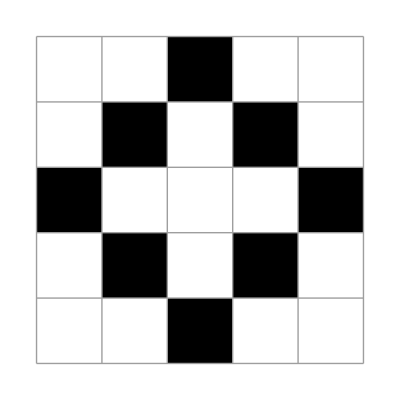
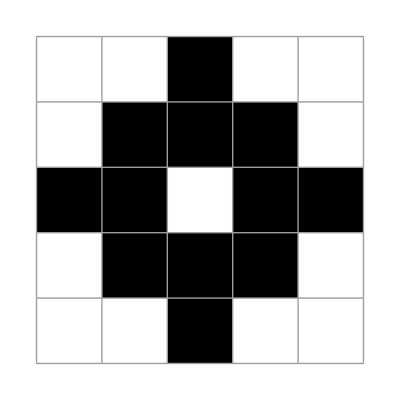
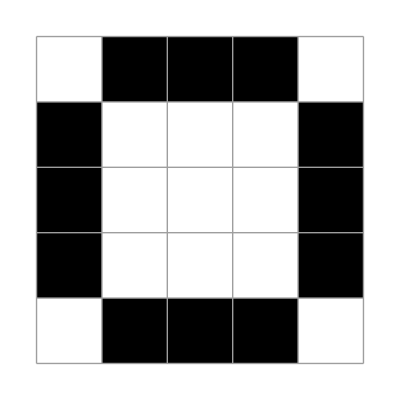

```mathematica
X0=({{xNW11, xN11, xN12, xN13, xNE13}, {xW11, x11, x12, x13, xE13}, {xW21, x21, x22, x23, xE23}, {xW31, x31, x32, x33, xE33}, {xSW31, xS31, xS32, xS33, xSE33}})/.endGame[[1]];
plt/@NestList[updateLife2[{5,5}][ #]&,
X0,3]
```